# Coil Examples

## Examples from Designing optimal loop, saddle, and ellipse-based magnetic coils by spherical harmonic mapping

Import the package:

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "Kernel", "CreateCoil.wl"}]]
```

## Loops

### Simple example: Anti-Helmholtz pair

Firstly, let’s optimize a anti-Helmholtz pair (also known as a Maxwell coil) consisting of a simple turn of radius ρ_c = 1 m carrying one amp of current generating the n=2 field harmonic existing between d_c = 0.01 ρ_c to d_c = ρ_c.

```mathematica
solutions =FindLoopCoil[{1},2, {0.01, 1}]
```

{{Coilχc[1]→0.866025,DesToErr→9.42734}}

### B_(2,0)

Let us optimize loops to generate the B_(2,0) field harmonic. First let’s examine what the B_x,B_y,and B_z components of this field harmonic are along the x-, y-, and z-axes.

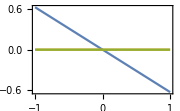
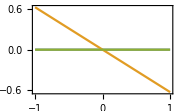
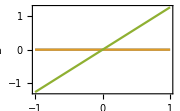

```mathematica
order = 2; (* Desired harmonic order *)
degree = 0; (* Desired harmonic degree *)
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
```

Let us define the known variables in our optimization of loop coils.

```mathematica
curr = {1, -2, 2}; (* Turn ratios (A) *)
χcmin = .1; (* Minimum normalized separation *)
χcmax = √3/2; (* Maximum normalized separation *)
ρc = 10 1*^-2; (* Coil radius (m) *)
```

We will now select the optimal positions of loops to maximize the n=2, m=0 field harmonic.

```mathematica
solutions =FindLoopCoil[curr,order, {χcmin, χcmax}]
```

{{Coilχc[1]→0.554372,Coilχc[2]→0.674766,Coilχc[3]→0.866025,DesToErr→34.5198},{Coilχc[1]→0.5531,Coilχc[2]→0.673608,Coilχc[3]→0.865142,DesToErr→33.5852},{Coilχc[1]→0.552599,Coilχc[2]→0.673065,Coilχc[3]→0.864629,DesToErr→33.2277},{Coilχc[1]→0.551441,Coilχc[2]→0.671812,Coilχc[3]→0.863445,DesToErr→32.4277},{Coilχc[1]→0.549406,Coilχc[2]→0.669616,Coilχc[3]→0.861379,DesToErr→31.1048},{Coilχc[1]→0.549032,Coilχc[2]→0.669214,Coilχc[3]→0.861001,DesToErr→30.8729},{Coilχc[1]→0.547837,Coilχc[2]→0.66793,Coilχc[3]→0.859797,DesToErr→30.1515},{Coilχc[1]→0.546613,Coilχc[2]→0.666618,Coilχc[3]→0.858569,DesToErr→29.4437},{Coilχc[1]→0.545779,Coilχc[2]→0.665726,Coilχc[3]→0.857737,DesToErr→28.9793},{Coilχc[1]→0.543812,Coilχc[2]→0.663628,Coilχc[3]→0.855782,DesToErr→27.9345}}

We have identified the ten coils which null the n=4 and n=6 field harmonics while maximizing the strength of the desired field harmonic compared to that of the leading-order error. In this case, DesToErr, is the magnitude of the desired field harmonic of order n=2 divided by the magnitude of the leading-order error field harmonic of order n=8.

We select the set of loops which maximize the value of this ratio:

```mathematica
χcopt ={Coilχc[1],Coilχc[2],Coilχc[3]} /. solutions[[1]]
```

{0.554372,0.674766,0.866025}

Let’s create a plot of the optimal set of loops on the surface of the coil cylinder.

```mathematica
LoopCoilPlot[χcopt,curr, ρc,order]
```

Let’s examine the B_x,B_y,and B_zcomponents of the magnetic field along the x-, y-, and z-axes.

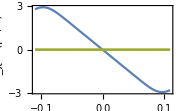
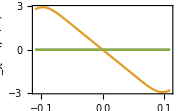
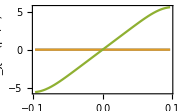

```mathematica
LoopFieldPlot[χcopt,curr, ρc,order,ImageSize->Small]
```

We can also plot the B_x,B_y,and B_zcomponents of the magnetic field generated by the coils along the xz-plane. We’ll modify the plot range so we only display the values of the field between [–6, 6] µT.

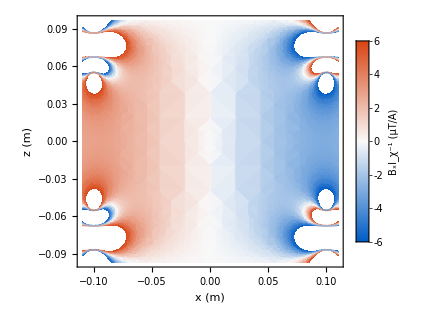
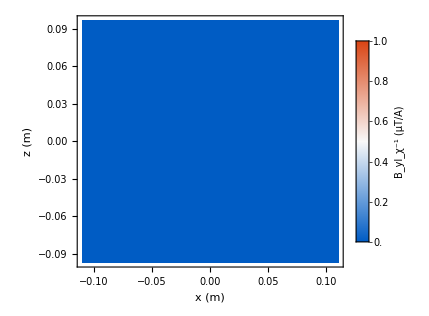
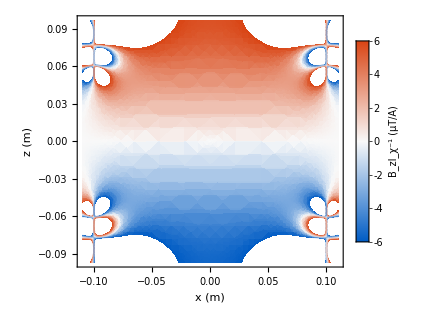

```mathematica
LoopFieldPlot2D[χcopt,curr, ρc,order, PlotRange->{Full,Full,{-6,6}}]
```

## Saddles

### B_(2,1)

Let us optimize saddles to generate the B_(2,1)field harmonic. First let’s examine what the B_x,B_y,and B_z components of this field harmonic are along the x-, y-, and z-axes.

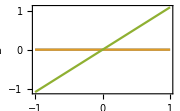
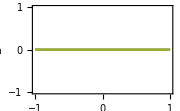
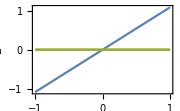

```mathematica
order = 2; (* Desired harmonic order *)
degree = 1; (* Desired harmonic degree *)
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
```

Let us define the known variables in our optimization of saddle coils. Note that our saddle pair is generating an axially symmetric harmonic, so there must be an even number of axial turn ratios and each turn ratio must connect to another with an equal and opposite current flow direction.

```mathematica
curr = {1,-1,1,-1}; (* Axial turn ratios (A) *)
azextents =2; (* Number of azmuthal arcs per saddle *)
χcmin = .1; (* Minimum normalized separation *)
χcmax = 2.56; (* Maximum normalized separation *)
ρc = 10 1*^-2; (* Coil radius (m) *)
```

We will now select the optimal azimuthal extents and axial separations of sets of saddles to maximize the n=2, m=1 field harmonic.

```mathematica
solutions =FindSaddleCoil[curr, {order, degree},azextents,{χcmin,χcmax}]
```

<|AxialSeparations→{{Coilχc[1]→0.2995,Coilχc[2]→0.417035,Coilχc[3]→0.654955,Coilχc[4]→2.5558,DesToErr→13.2438},{Coilχc[1]→0.299514,Coilχc[2]→0.417045,Coilχc[3]→0.654995,Coilχc[4]→2.54896,DesToErr→13.2418},{Coilχc[1]→0.299538,Coilχc[2]→0.417063,Coilχc[3]→0.655069,Coilχc[4]→2.53669,DesToErr→13.2381},{Coilχc[1]→0.299551,Coilχc[2]→0.417072,Coilχc[3]→0.655106,Coilχc[4]→2.5307,DesToErr→13.2361},{Coilχc[1]→0.299573,Coilχc[2]→0.417088,Coilχc[3]→0.655173,Coilχc[4]→2.52024,DesToErr→13.2325},{Coilχc[1]→0.299573,Coilχc[2]→0.417088,Coilχc[3]→0.655174,Coilχc[4]→2.52007,DesToErr→13.2325},{Coilχc[1]→0.299589,Coilχc[2]→0.4171,Coilχc[3]→0.655223,Coilχc[4]→2.51282,DesToErr→13.2299},{Coilχc[1]→0.299595,Coilχc[2]→0.417104,Coilχc[3]→0.655239,Coilχc[4]→2.51045,DesToErr→13.229},{Coilχc[1]→0.299609,Coilχc[2]→0.417115,Coilχc[3]→0.655283,Coilχc[4]→2.50396,DesToErr→13.2265},{Coilχc[1]→0.299623,Coilχc[2]→0.417124,Coilχc[3]→0.655324,Coilχc[4]→2.49811,DesToErr→13.2242}},AzimuthalExtents→{{Coilϕc[1]→0.733038,Coilϕc[2]→1.36136},{Coilϕc[1]→0.10472,Coilϕc[2]→1.15192},{Coilϕc[1]→0.733038,Coilϕc[2]→1.78024}}|>

Here, we’ve identified the sets of axial saddle positions which null the field harmonic orders n=4,6,8 and maximize the ratio of the magnitude of the desired field harmonic of order n=2 to the leading-order error n=10. Simultaneously, we have optimized the azimuthal extent of arcs to null the field harmonic degrees m=3,5. This means that, when we evaluate the desired-to-leading-order-magnitude ratio, we evaluate the ratio of the magnitude of the harmonic of order n=2 and degree m=1 to that of order n=10 and degree m=1.

We select the set of saddles which maximize this ratio:

```mathematica
χcopt ={Coilχc[1],Coilχc[2],Coilχc[3],Coilχc[4]} /. solutions[[1,1]]
ϕcopt ={Coilϕc[1],Coilϕc[2]} /. solutions[[2,1]]
```

{0.2995,0.417035,0.654955,2.5558}

{0.733038,1.36136}

Let’s create a plot of the optimal set of saddles on the surface of the coil cylinder.

```mathematica
SaddleCoilPlot[χcopt,ϕcopt,curr,ρc,{order,degree}]
```

Let’s examine each magnetic field component along the x-, y-, and z- axes:

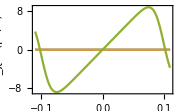
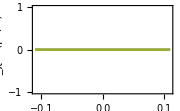
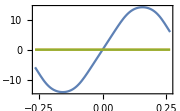

```mathematica
SaddleFieldPlot[χcopt,ϕcopt,curr,ρc,{order,degree},ImageSize->Small]
```

We can also plot the B_x,B_y,and B_zcomponents of the magnetic field generated by the coils along the xz-plane. Let’s plot them this time with a Blue–Green–Yellow color scheme.

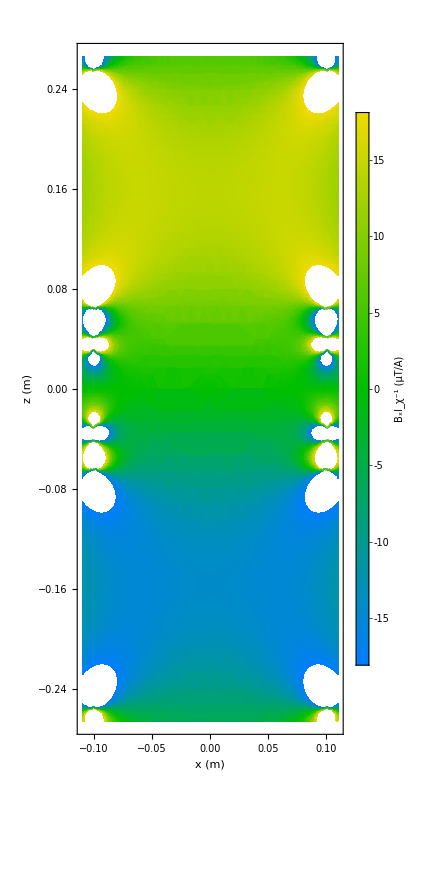
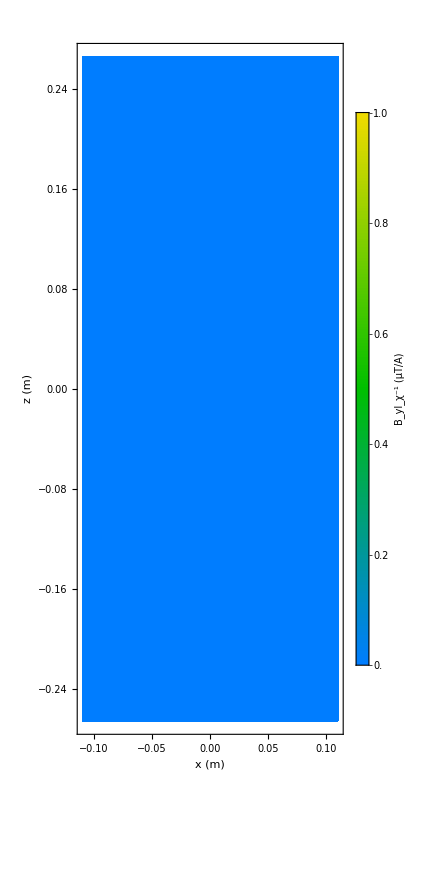
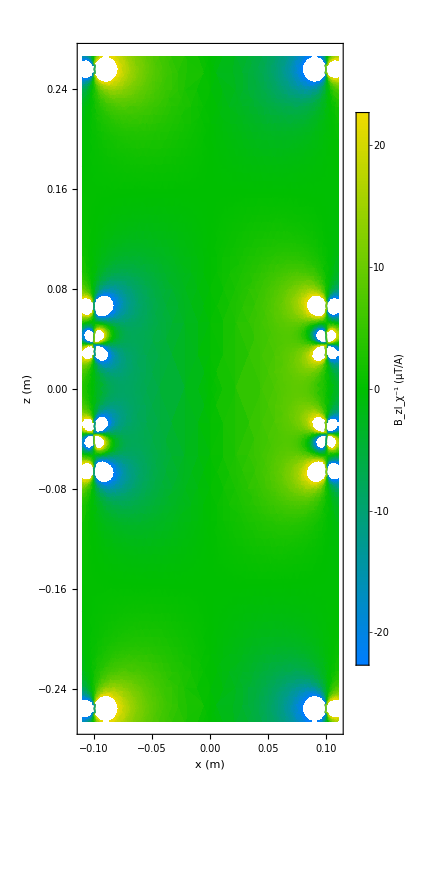

```mathematica
SaddleFieldPlot2D[χcopt,ϕcopt,curr,ρc,{order,degree},ColorFunction->(Blend[{RGBColor[0, 0.49, 1],RGBColor[0, 0.75, 0],RGBColor[0.94, 0.86, 0]},#]&)]
```

## Ellipses

### B_(2,1)

Let us define the known variables in our optimization of ellipse coils.

```mathematica
curr = {1,-1}; (* Turn ratios (A) *)
order = 2; degree = 1;(* Desired harmonic order and degree *)
χcmin = .1; (* Minimum normalized separation *)
χcmax = 1.32; (* Maximum normalized separation *)
ψcmin = .1; (* Minimum normalized elextent *)
ψcmax = .5; (* Maximum normalized extent *)
ρc = 10 1*^-2;(* Coil radius (m) *)
```

We will now select the optimal axial separations and extents of sets of ellipses to maximize the n=2, m=1 field harmonic.

```mathematica
solutions =FindEllipseCoil[curr,{order, degree},{χcmin,χcmax},{ψcmin,ψcmax},
(* Use non-default option values in this case for computational run-time: *)
"MeshPointsPerχc"->8,"InterpolationPoints"->3,"MinSeparationAndExtentDifference"->0,"ContourMeshNN"->1,"NulledHarmonics"->{{4,1}},"LeadingErrorHarmonic"->{6,1}]
```

{{Coilχc[1]→0.684225,Coilχc[2]→0.749289,Coilψc[1]→0.284244,Coilψc[2]→0.403639,DesToErr→79233.1},{Coilχc[1]→0.479388,Coilχc[2]→0.578387,Coilψc[1]→0.300762,Coilψc[2]→0.463785,DesToErr→3637.06},{Coilχc[1]→0.537072,Coilχc[2]→0.5746,Coilψc[1]→0.323002,Coilψc[2]→0.384021,DesToErr→1812.49},{Coilχc[1]→0.5073,Coilχc[2]→0.612208,Coilψc[1]→0.276759,Coilψc[2]→0.44532,DesToErr→1523.47},{Coilχc[1]→0.494428,Coilχc[2]→0.509759,Coilψc[1]→0.380522,Coilψc[2]→0.407276,DesToErr→1062.24},{Coilχc[1]→0.593683,Coilχc[2]→0.743838,Coilψc[1]→0.218891,Coilψc[2]→0.472187,DesToErr→1038.07},{Coilχc[1]→0.568439,Coilχc[2]→0.672977,Coilψc[1]→0.252665,Coilψc[2]→0.425128,DesToErr→1032.05},{Coilχc[1]→0.461627,Coilχc[2]→0.551952,Coilψc[1]→0.323995,Coilψc[2]→0.480931,DesToErr→834.544},{Coilχc[1]→0.479132,Coilχc[2]→0.550403,Coilψc[1]→0.328117,Coilψc[2]→0.448515,DesToErr→799.134},{Coilχc[1]→0.591347,Coilχc[2]→0.645635,Coilψc[1]→0.285984,Coilψc[2]→0.376809,DesToErr→717.541}}

Here, we’ve identified the sets of ellipse separations and extents which maximize the ratio of the magnitude of the desired-to-leading-order-error total field harmonic. Specifically, this is the ratio of the field harmonic of order n=2 and degree m=1 compared to that of order n=6 and degree m=1 as the field harmonic of order n=4 and degree m=1 is already nulled.

Like before, let’s extract the solution that maximizes this ratio:

```mathematica
χcopt ={Coilχc[1],Coilχc[2]} /. solutions[[1]]
ψcopt ={Coilψc[1],Coilψc[2]} /. solutions[[1]]
```

{0.684225,0.749289}

{0.284244,0.403639}

```mathematica
EllipseCoilPlot[{{χcopt[[1]],ψcopt[[1]]},{χcopt[[2]],ψcopt[[2]]}} ,curr,ρc,{order,degree}]
```

Let’s examine each magnetic field component along the x-, y-, and z- axes:

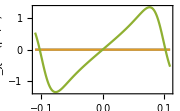
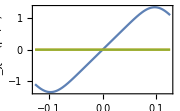
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EllipseFieldPlot[{{χcopt[[1]],ψcopt[[1]]},{χcopt[[2]],ψcopt[[2]]}} ,curr,ρc,{order,degree},ImageSize->Small]
```

We can also plot the B_x,B_y,and B_zcomponents of the magnetic field generated by the coils along the xz-plane.

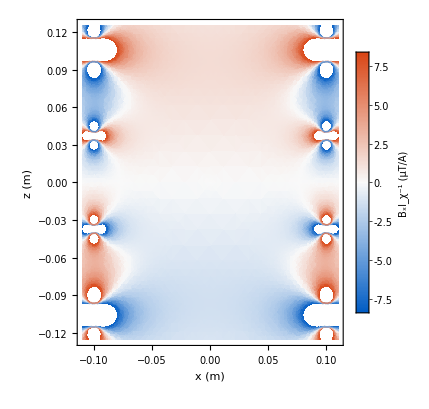
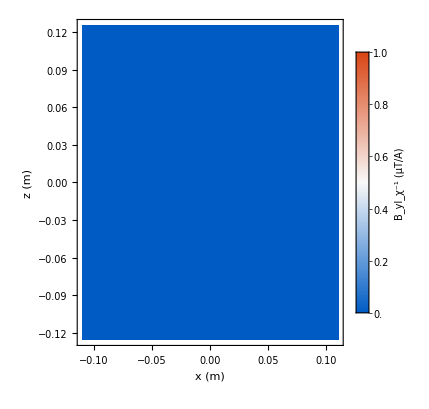
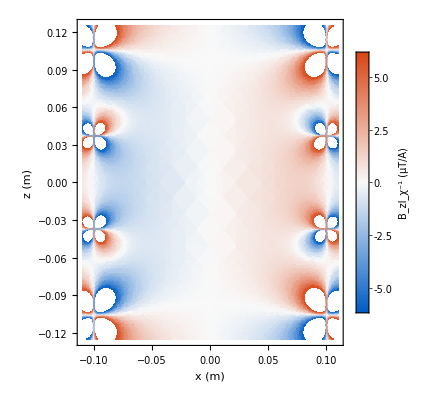

```mathematica
EllipseFieldPlot2D[{{χcopt[[1]],ψcopt[[1]]},{χcopt[[2]],ψcopt[[2]]}} ,curr,ρc,{order,degree}]
```

## Supplementary Coil Designs

### B_(1,0)

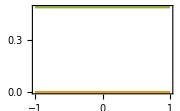
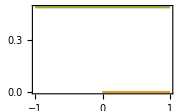
{-Graphics-,-Graphics-,-Graphics-}

{Coilχc[1]→0.453652,Coilχc[2]→0.945434,DesToErr→10.3162}

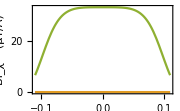
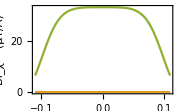
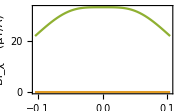

```mathematica
curr = {3,1}; order = 1; degree = 0; χcmin = .1;χcmax = 0.95;ρc = 10 1*^-2;
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
solution =FindLoopCoil[curr, order,{χcmin,χcmax},"CoilsReturned"->1][[1]]
LoopCoilPlot[solution,curr, ρc,order]
LoopFieldPlot[solution,curr, ρc,order, ImageSize->Small]
```

### B_(3,0)

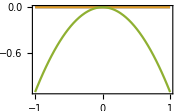
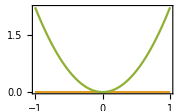
{-Graphics-,-Graphics-,-Graphics-}

{Coilχc[1]→0.377471,Coilχc[2]→0.901987,DesToErr→2265.09}

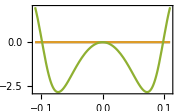
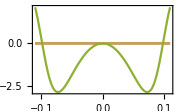
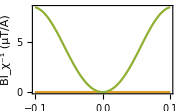

```mathematica
curr = {-1,2}; order = 3; degree=0; χcmin = .1;χcmax = 0.95;ρc = 10 1*^-2;
HarmonicFieldPlot[{order, degree}, ImageSize->Small]
solution =FindLoopCoil[curr, order,{χcmin,χcmax},"CoilsReturned"->1][[1]]
LoopCoilPlot[solution,curr, ρc,order]
LoopFieldPlot[solution,curr, ρc,order, ImageSize->Small]
```